# Riemann Prime Counting Function

### Author

Eric W. Weisstein
August 22, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/PrimeNumbers/RiemannPrimeCountingFunction.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/RiemannPrimeCountingFunction.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
RiemannFIntegral[x_?NumericQ,opts___?OptionQ]:=NIntegrate[1/(t Log[t](t^2-1)),{t,x,∞},opts]

RiemannFSum[x_?NumericQ]:=Total[PrimePi[x^(1/#)]/#&/@Range[Floor[Log[2,x]]]]

MyRiemannR[x_?NumericQ,m_?Positive,opts___?OptionQ]:=NSum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,m},opts]
MyRiemannR[x_?NumericQ,opts___?OptionQ]:=MyRiemannR[x,Infinity,opts]

GramSeries[x_?NumericQ,m_,opts___?OptionQ]:=1+NSum[Log[x]^k/k/k!/Zeta[k+1],{k,m},opts]
GramSeries[x_?NumericQ]:=GramSeries[x,Infinity]
```

## f(x)

```mathematica
Integrate[1/(t Log[t](t^2-1)),{t,x,∞}]
```

∫_x^∞ 1/(t (-1+t^2) Log[t])ⅆt

### Minimum Numerically

#### v5

```mathematica
RiemannFIntegral[2]
```

0.14001

```mathematica
RiemannFIntegral[2,WorkingPrecision->30]
```

0.14001010114328692669

```mathematica
RiemannFIntegral[2,WorkingPrecision->200,MaxRecursion->15]//Timing
```

{13.16 Second,0.1400101011432869266869173052342997331775279281270658289489468743113049149951613610276026532064866696343450744421081484565062628631720335126906534034078419206465417262549675852460323007364899}

```mathematica
RiemannFIntegral[2,WorkingPrecision->250,MaxRecursion->15]//Timing
```

{24.35 Second,0.140010101143286926686917305234299733177527928127065828948946874311304914995161361027602653206486669634345074442108148456506262863172033512690653403407841920646541726254967585246032300736489862896587065609690369779504470973081723506081850455}

```mathematica
RiemannFIntegral[2,WorkingPrecision->300,MaxRecursion->15]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

$Aborted

...hangs...

#### v6

```mathematica
RiemannFIntegral[2,WorkingPrecision->200,MaxRecursion->15]//Timing
```

{2.95 Second,0.14001010114328692668691730523429973317752792812706582894894687431130491499516136102760265320648666963434507444210814845650626286317203351269065340340784192064654172625496758524603230073648986289658707}

```mathematica
RiemannFIntegral[2,WorkingPrecision->250,MaxRecursion->15]//Timing
```

{4.13 Second,0.1400101011432869266869173052342997331775279281270658289489468743113049149951613610276026532064866696343450744421081484565062628631720335126906534034078419206465417262549675852460323007364898628965870656096903697795044709730817235060818504551403552755}

```mathematica
RiemannFIntegral[2,WorkingPrecision->300,MaxRecursion->15]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 200 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the difference between the values of PrecisionGoal and WorkingPrecision is too small; the integrand is highly oscillatory or it is not a (piecewise) smooth function; the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxNumberOfErrorIncreases might lead to a convergent numerical integration.

{32.74 Second,0.140010101143286926686917305234299733177527928127065828948946874311304914995161361027602653206486669634345074442108148456506262863172033512690653403407841920646541726254967585246032300736489862896587065609690369779504470973081723431962859999932087786003917525814185201995658387513167324163915286823708}

### Minimum Symbolically

#### v4.2.1

```mathematica
Integrate[1/(t Log[t](t^2-1)),{t,2,∞}]
```

∫_2^∞ 1/(t (-1+t^2) Log[t])ⅆt

#### v5

```mathematica
Integrate[1/(t Log[t](t^2-1)),{t,2,∞}]
```

∫_2^∞ 1/(t (-1+t^2) Log[t])ⅆt

#### v6

```mathematica
Integrate[1/(t Log[t](t^2-1)),{t,2,∞}]
```

∫_2^∞ 1/(t (-1+t^2) Log[t])ⅆt

### Plot

```mathematica
<<Utilities`Typesetting`
```

```mathematica
MakeBoxes[label1,TraditionalForm]:=FractionBox["1",RowBox[{"t"," ",RowBox[{"(",RowBox[{SuperscriptBox["t","2"],"-","1"}],")"}]}]]
```

```mathematica
MakeBoxes[label2,TraditionalForm]:=RowBox[{SubsuperscriptBox["∫","x","∞"],RowBox[{FractionBox[RowBox[{"d","t"}],RowBox[{"t"," ",RowBox[{"(",RowBox[{SuperscriptBox["t","2"],"-","1"}],")"}]}]]}]}]
```

#### V5

```mathematica
Show[GraphicsArray[Block[{$DisplayFunction=Identity},
{
Plot[1/(t Log[t](t^2-1)),{t,0,5},PlotStyle->Red,PlotRange->{0,5},
AxesLabel->TraditionalForm/@{t,label1}],
Plot[RiemannFIntegral[x],{x,1,5},PlotStyle->Red,PlotRange->{0,5},AxesLabel->TraditionalForm/@{x,label2}]
}
]],GraphicsSpacing->-.1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in t near t = 1.. More…

⁃GraphicsArray⁃

#### V7

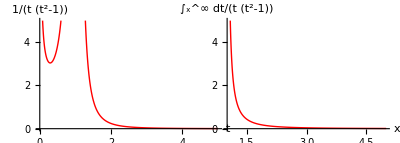

```mathematica
GraphicsGrid[{{Plot[1/(t Log[t](t^2-1)),{t,0,5},PlotStyle->Red,PlotRange->{0,5},
AxesLabel->TraditionalForm/@{t,label1}],
Plot[RiemannFIntegral[x],{x,1,5},PlotStyle->Red,PlotRange->{0,5},AxesLabel->TraditionalForm/@{x,label2}]
}},Spacings->-100,ImageSize->400]
```

### Other Form

```mathematica
RiemannFSum2[n_]:=Plus@@Flatten[1/Range[Floor[Log[#,n]]]&/@Prime[Range[PrimePi[n]]]]
```

```mathematica
RiemannFSum2/@Range[10]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3}

### Values

```mathematica
PrimePi[2]
```

1

```mathematica
Solve[x^(1/n)==2,n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{n→Log[x]/Log[2]}}

```mathematica
RiemannFSum/@Range[10]//InputForm
```

{0, 1, 2, 5/2, 7/2, 7/2, 9/2, 29/6, 16/3, 16/3}

```mathematica
RiemannFSum/@Range[20]
```

{0,1,2,5/2,7/2,7/2,9/2,29/6,16/3,16/3,19/3,19/3,22/3,22/3,22/3,91/12,103/12,103/12,115/12,115/12}

```mathematica
MapIndexed[{#2[[1]]+1,#1}&,-Subtract@@@Partition[RiemannFSum/@Range[20],2,1]]
```

{{2,1},{3,1},{4,1/2},{5,1},{6,0},{7,1},{8,1/3},{9,1/2},{10,0},{11,1},{12,0},{13,1},{14,0},{15,0},{16,1/4},{17,1},{18,0},{19,1},{20,0}}

```mathematica
Through[{Numerator,Denominator}[RiemannFSum/@Range[20]]]
```

{{0,1,2,5,7,7,9,29,16,16,19,19,22,22,22,91,103,103,115,115},{1,1,1,2,2,2,2,6,3,3,3,3,3,3,3,12,12,12,12,12}}

```mathematica
<<Utilities`Plot`
```

```mathematica
Show[Block[{$DisplayFunction=Identity},{IntegerListPlot[PrimePi[Range[50]],PlotStyle->Black],IntegerListPlot[RiemannFSum/@Range[50]]}
],AxesLabel->TraditionalForm/@{x,{StyleForm[HoldForm[f[x]],FontColor->Red],StyleForm[PrimePi[x],FontColor->Black]}}]
```

⁃Graphics⁃

### Inversion

```mathematica
pi[x_]:=Plus@@(RiemannFSum[x^(1/#)]MoebiusMu[#]/#&/@Range[Floor[Log[2,x]]])
```

```mathematica
pi/@Range[20]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8}

```mathematica
PrimePi/@Range[20]
```

{0,1,2,2,3,3,4,4,4,4,5,5,6,6,6,6,7,7,8,8}

```mathematica
Plot[pi[x]-PrimePi[x],{x,0,100},PlotStyle->Red]
```

⁃Graphics⁃

### Connection With ζ(s)

```mathematica
<<Utilities`Plot`
```

```mathematica
ComplexPlot3D[Log[Zeta[s]]/s,{s,-5,5},PlotPoints->150]//Timing
```

Power::infy: Infinite expression 1/0. encountered. More…

{7.35 Second,⁃GraphicsArray⁃}

```mathematica
ComplexContourPlot[Log[Zeta[s]]/s,{s,-5,5}]//Timing
```

Power::infy: Infinite expression 1/0. encountered. More…

⁃GraphicsArray⁃

```mathematica
Plot[Log[Zeta[s]]/s,{s,1,5},PlotStyle->Red]
```

⁃Graphics⁃

```mathematica
g[s_,opts___?OptionQ]:=NIntegrate[RiemannFSum[x] x^(-s-1),{x,0,∞},opts]
```

```mathematica
Plot[g[s,WorkingPrecision->10]-Log[Zeta[s]]/s,{s,1.9,5},PlotStyle->Red]//Timing
```

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-1.9 - 1) is less than WorkingPrecision (10.). More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-1.9 - 1) is less than WorkingPrecision (10.). More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-2.02576 - 1) is less than WorkingPrecision (10.). More…

General::stop: Further output of NIntegrate :: "precw" will be suppressed during this calculation. More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

General::stop: Further output of NIntegrate :: "ncvb" will be suppressed during this calculation. More…

{5.16 Second,⁃Graphics⁃}

```mathematica
Plot[g[s,WorkingPrecision->20]-Log[Zeta[s]]/s,{s,1.9,10},PlotStyle->Red]//Timing
```

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-1.9 - 1) is less than WorkingPrecision (20.). More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-1.9 - 1) is less than WorkingPrecision (20.). More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

NIntegrate::precw: The precision of the argument function (RiemannFSum[x]\ x^-2.22859 - 1) is less than WorkingPrecision (20.). More…

General::stop: Further output of NIntegrate :: "precw" will be suppressed during this calculation. More…

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration being 0, oscillatory integrand, or insufficient WorkingPrecision. If your integrand is oscillatory try using the option Method->Oscillatory in NIntegrate. More…

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation. More…

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 7 recursive bisections in x near x = 2.01176. More…

General::stop: Further output of NIntegrate :: "ncvb" will be suppressed during this calculation. More…

{15.01 Second,⁃Graphics⁃}

## Riemann's R(x)

### ∑_n^∞ (μ(n) li(x^(1/n)))/n

```mathematica
Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,k}]
```

∑_n^k (LogIntegral[x^(1/n)] MoebiusMu[n])/n

```mathematica
TimeConstrained[Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,∞}],60]//Timing
```

{14.6914,∑_n^∞ (LogIntegral[x^(1/n)] MoebiusMu[n])/n}

```mathematica
RiemannR[10^-20.]
```

17.2099

```mathematica
N[RiemannR[10^-20],10]
```

0.000221321328

### ∑_k^∞ (ln^k(x))/(k k! ζ(k+1))+1

```mathematica
N[With[{x=10^-20},1+Sum[Log[x]^k/k/k!/Zeta[k+1],{k,10^3}]],10]
```

0.000221321328

```mathematica
N[RiemannR[10^-20],10]
```

0.000221321328

```mathematica
1+Sum[Log[x]^k/k/k!/Zeta[k+1],{k,m}]
```

1+∑_k^m Log[x]^k/(k k! Zeta[1+k])

```mathematica
1+Sum[Log[x]^k/k/k!/Zeta[k+1],{k,∞}]
```

1+∑_k^∞ Log[x]^k/(k k! Zeta[1+k])

### Series

```mathematica
Series[RiemannR[x],{x,0,3}]
```

RiemannR[0]+RiemannR'[0] x+1/2 RiemannR''[0] x^2+1/6 RiemannR^(3)[0] x^3+O[x]^4

### Special Values

```mathematica
Limit[RiemannR[x],x->0]
```

RiemannR[0]

```mathematica
RiemannR[0]
```

RiemannR[0]

```mathematica
With[{x=0},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,k}]]
```

0

```mathematica
With[{x=0},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,∞}]]
```

$Aborted

### Plots

#### V6

Use the Gram series instead because the Riemann series has bad convergence properties

```mathematica
Plot[GramSeries[x]-PrimePi[x],{x,0,1000},
PlotStyle->Red,
AxesLabel->TraditionalForm/@{x,R[x]-PrimePi[x]}
]//Timing
```

{173.55 Second,⁃Graphics⁃}

#### V7

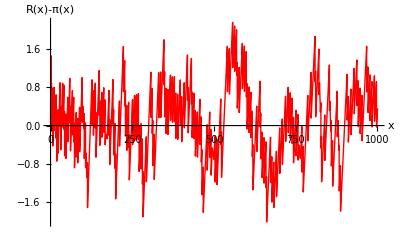

```mathematica
Plot[RiemannR[x]-PrimePi[x],{x,0,1000},PlotStyle->Red,AxesLabel->{x,R[x]-PrimePi[x]}]
```

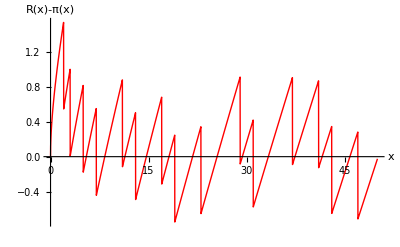

```mathematica
Plot[RiemannR[x]-PrimePi[x],{x,0,50},PlotStyle->Red,AxesLabel->{x,R[x]-PrimePi[x]}]
```

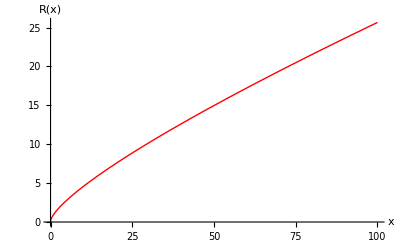

```mathematica
g1=Plot[RiemannR[t],{t,0,100},AxesLabel->{x,R[x]},PlotStyle->Red]
```

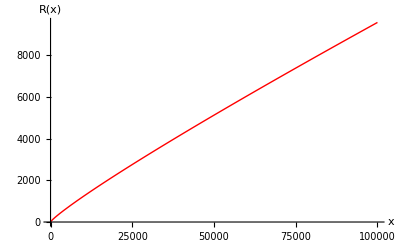

```mathematica
g11=Plot[RiemannR[t],{t,0,10^5},AxesLabel->{x,R[x]},PlotStyle->Red]
```

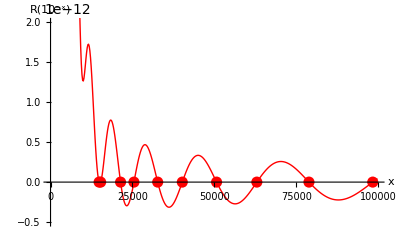

```mathematica
g2=ListPlot[l,Joined->True,PlotRange->{All,{-.5*^-12,2*^-12}},AxesOrigin->{0,0},PlotStyle->Red,AxesLabel->{x,R[10^-x]},Epilog->{Red,PointSize[.02],Point[{#,0}&/@roots]}]
```

```mathematica
m=t/.FindRoot[RiemannR[10^-t],{t,14000},WorkingPrecision->20]
```

14827.737871008076586

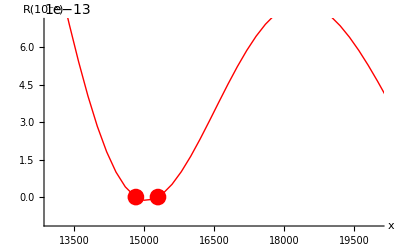

```mathematica
g3=ListPlot[l,Joined->True,PlotRange->{{13000,20000},{-.1*^-12,.7*^-12}},PlotStyle->Red,AxesLabel->{x,R[10^-x]},Epilog->{Red,PointSize[.03],Point[{#,0}&/@roots]}]
```

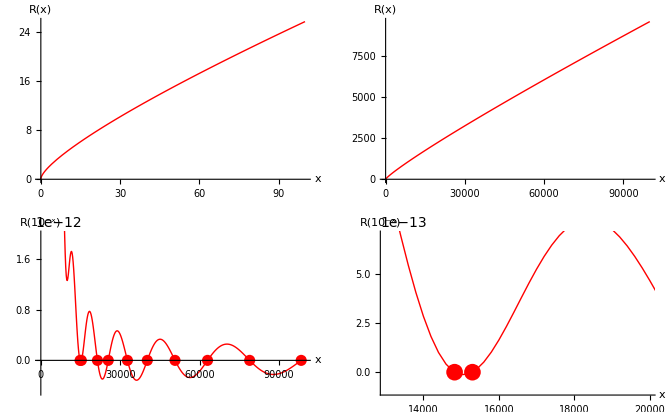

```mathematica
GraphicsGrid[{{g1,g11},{g2,g3}}]
```

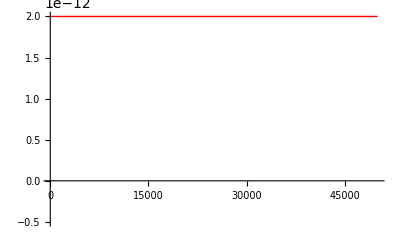

```mathematica
bug=Plot[RiemannR[10^-t],{t,1,50000},WorkingPrecision->10,PlotRange->{All,{-.5*^-12,2*^-12}},PlotPoints->20,AxesOrigin->{0,0},PlotStyle->Red]
```

#### Difference Between Numerical Convergence of G[x] and R[x]

```mathematica
Plot[Evaluate[GramSeries[x]-Append[Table[RiemannR[x,10^n],{n,5}],RiemannR[x]]],{x,0,20},PlotStyle->{Blue,Green,Yellow,Orange,Red,Black},
PlotRange->All,
AxesLabel->TraditionalForm/@{x,G[x]-R[x]}]//Timing
```

{353.27 Second,⁃Graphics⁃}

#### v4.2.1

```mathematica
RiemannR[10]//Timing
```

{0.22 Second,4.49773}

```mathematica
RiemannR[10,Method->Fit]//Timing
```

{0. Second,4.49773}

```mathematica
RiemannR[10,Method->Fit,VerifyConvergence->False]//Timing
```

{0.01 Second,4.49773}

#### v5

```mathematica
RiemannR[10]//Timing
```

{26.56 Second,4.49773}

```mathematica
RiemannR[10,Method->Fit]//Timing
```

{0.01 Second,4.49773}

```mathematica
RiemannR[10,Method->Fit,VerifyConvergence->False]//Timing
```

{0.01 Second,4.49773}

#### v5.1

```mathematica
RiemannR[10]//Timing
```

{36.04 Second,4.49773}

```mathematica
RiemannR[10,Method->Fit]//Timing
```

{0.01 Second,4.49773}

```mathematica
RiemannR[10,Method->Fit,VerifyConvergence->False]//Timing
```

{0.02 Second,4.49773}

#### V7

```mathematica
Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,k}]//InputForm
```

Sum[(LogIntegral[x^n^(-1)]*MoebiusMu[n])/n, {n, k}]

```mathematica
Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,∞}]//InputForm
```

Sum[(LogIntegral[x^n^(-1)]*MoebiusMu[n])/n, {n, Infinity}]

```mathematica
Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,10^4}]/.x->10.
```

4.58085

```mathematica
RiemannR[10.]
```

4.56458

### Zeros

```mathematica
l=N[Table[{t,RiemannR[10^-t]},{t,1,100000,200}],5];//Timing
```

{22.5321,Null}

```mathematica
Map[First,Select[Partition[l,2,1],Unequal@@(Sign[Last/@#])&],{2}]
```

{{14801.,15001.},{15201.,15401.},{21201.,21401.},{25401.,25601.},{32601.,32801.},{40201.,40401.},{50601.,50801.},{62801.,63001.},{78801.,79001.},{98201.,98401.}}

```mathematica
FindRoot[RiemannR[10^-x],{x,14801.`5.,15001.`5.}]
```

{x→14827.7}

```mathematica
roots=x/.FindRoot[RiemannR[10^-x],{x,Sequence@@Round[#]},WorkingPrecision->20]&/@Map[First,Select[Partition[l,2,1],Unequal@@(Sign[Last/@#])&],{2}]
```

{14827.737871008076586,15300.690468335228669,21381.482880022267012,25461.69876139225958,32711.861969368661949,40219.623763667380594,50689.847595403997023,62979.790849929919454,78890.16524225080263,98357.799186896950333}

```mathematica
N[roots,6]
```

{14827.7,15300.7,21381.5,25461.7,32711.9,40219.6,50689.8,62979.8,78890.2,98357.8}

```mathematica
N[10^-roots,4]
```

{1.829×10^-14828,2.04×10^-15301,3.289×10^-21382,2.001×10^-25462,1.374×10^-32712,2.378×10^-40220,1.42×10^-50690,1.619×10^-62980,6.835×10^-78891,1.588×10^-98358}

```mathematica
root1=x/.FindRoot[RiemannR[10^-x],{x,Sequence@@Round[#]},WorkingPrecision->110]&/@{First[Map[First,Select[Partition[l,2,1],Unequal@@(Sign[Last/@#])&],{2}]]}
```

{14827.737871008076585863844477060593120271712925032542514088647834200317237279860191140116528810559513807564386}

### Gram Series

```mathematica
1+Sum[Log[x]^k/k/k!/Zeta[k+1],{k,∞}]//InputForm
```

1 + Sum[Log[x]^k/(k*k!*Zeta[1 + k]), {k, Infinity}]

```mathematica
1+NSum[Log[x]^k/k/k!/Zeta[k+1],{k,∞}]/.x->10.
```

NSum::nsnum: Summand (or its derivative) Log[x]^k/(k k !) Zeta[k + 1] is not numerical at point k = 16.

4.56458

```mathematica
RiemannR[10.]
```

4.56458

### Computation

#### n=1

```mathematica
N[GramSeries[1]]
```

1.

```mathematica
N[RiemannR[1.00000000001]]
```

-0.0470428

#### n=10

```mathematica
N[GramSeries[10]]
```

4.56458

```mathematica
RiemannR[10,WorkingPrecision->20]
```

4.497733378170266057

```mathematica
RiemannR[10,NSumExtraTerms->50,NSumTerms->50]
```

4.46693

```mathematica
With[{x=10.},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,10^5}]]//Timing
```

{13.13 Second,4.56948}

```mathematica
N[With[{x=10},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,10^4}]],20]//Timing
```

{18.18 Second,4.5808535000894562792}

```mathematica
N[With[{x=10},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,10^5}]],20]//Timing
```

{185.67 Second,4.5694802101137963227}

```mathematica
N[With[{x=10},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n,5 10^5}]],20]//Timing
```

{966.78 Second,4.5645147449783808556}

```mathematica
N[With[{x=10},Sum[MoebiusMu[n]/n LogIntegral[x^(1/n)],{n ,10^6}]],20]//Timing
```

{1707.61 Second,4.5620809396422096858}

```mathematica
NSum[MoebiusMu[n]/n LogIntegral[10^(1/n)],{n,Infinity},Method->Fit,VerifyConvergence->False]
```

NSum[(MoebiusMu[n] LogIntegral[10^(1/n)])/n,{n,∞},Method→Fit,VerifyConvergence→False]

### Oscillatory behavior of R(x)

```mathematica
ListPlot[Table[With[{x=10.},MoebiusMu[n]/n LogIntegral[x^(1/n)]],{n,10^3}],Joined->True,PlotStyle->Red]
```

⁃Graphics⁃

```mathematica
ListPlot[Table[With[{x=10.},MoebiusMu[n]/n LogIntegral[x^(1/n)]],{n,10^5,10^5+10^3}],Joined->True,PlotStyle->Red]
```

⁃Graphics⁃

```mathematica
ListPlot[Table[With[{x=10.},MoebiusMu[n]/n LogIntegral[x^(1/n)]],{n,10^6,10^6+10^3}],Joined->True,PlotStyle->Red]
```

⁃Graphics⁃

A057793

```mathematica
Table[RiemannR[10^n],{n,20}]//Round//Timing
```

{4,26,168,1227,9587,78527,664667,5761552,50847455,455050683,4118052495,37607910542,346065531066,3204941731602,29844570495887,279238341360978,2623557157055980,24739954284239448,234057667300229504,2220819602556028160}

```mathematica
Round[Table[NGramSeries[10^n,WorkingPrecision->20],{n,20}]]
```

SequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect. (More…)

General::stop: Further output of SequenceLimit :: "seqlim" will be suppressed during this calculation. (More…)

{5,26,168,1227,9587,78527,664578,5765480,50789343,2727499194,16521447,21302570,551167687,-151181567,91684,18121580,65632568,-130075075,-71505754,-84096045}

```mathematica
Timing[v=Table[NGramSeries[10^n,WorkingPrecision->20,NSumTerms->100,
NSumExtraTerms->50],{n,23}];]
```

{1.3 Second,Null}

```mathematica
Round[v]
```

{5,26,168,1227,9587,78527,664667,5761552,50847455,455050683,4118052495,37607910542,346065531066,3204941731602,29844570495887,279238341360977,2623557157055978,24739954284239494,234057667300228940,2220819602556027015,21127269485932299724,201467286689188773625}

```mathematica
Take[Round[v],19]-{4,26,168,1227,9587,78527,664667,5761552,50847455,455050683, 4118052495,37607910542,346065531066,3204941731602,29844570495887,279238341360977,2623557157055978,24739954284239494,234057667300228940}
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PrimePi[10]
```

4

```mathematica
Abs[N[v-Round[v]]]
```

{0.435417,0.338367,0.359446,0.0687817,0.431739,0.399429,0.447565,0.13268,0.427721,0.306847,0.3686,0.22591,0.173973,0.310965,0.0726218,0.18723,0.00387546,0.402522,0.234657,0.401218,0.266136,0.}

```mathematica
v[[{1,16}]]//InputForm
```

{4.564583141005090239865774695583979`20.1074, 
 2.792383413609771872302539272982567`20*^14}

A057794

```mathematica
primepi={4,25,168,1229,9592,78498,664579,5761455,50847534,455052511,4118054813,37607912018,346065536839,3204941750802,29844570422669,279238341033925,2623557157654233, 24739954287740860,234057667276344607,2220819602560918840, 21127269486018731928,201467286689315906290,1925320391606818006727};
```

```mathematica
d=Round[v-primepi]
```

{1,1,0,-2,-5,29,88,97,-79,-1828,-2318,-1476,-5773,-19200,73218,327052,-598255,-3501366,23884333,-4891825,-86432204,-127132665,1019262049}

```mathematica
Abs[d]-{1,1,0,2,5,29,88,97,79,1828,2318,1476,5773,19200,73218, 327052,598255,3501366,23884333,4891825,86432204,127132665}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[{n,r=RiemannR[10^n,Method->Fit]-PrimePi[10^n],Round[r]},{n,5}]//ColumnForm
```

{1,0.497733,0}
{2,0.624077,1}
{3,0.340593,0}
{4,-2.07317,-2}
{5,-4.56042,-5}

#### V6

```mathematica
TableForm[Transpose[{Range[23],Round[v],Round[primepi-v]}],TableAlignments->Right]
```

1 | 5 | -1
2 | 26 | -1
3 | 168 | 0
4 | 1227 | 2
5 | 9587 | 5
6 | 78527 | -29
7 | 664667 | -88
8 | 5761552 | -97
9 | 50847455 | 79
10 | 455050683 | 1828
11 | 4118052495 | 2318
12 | 37607910542 | 1476
13 | 346065531066 | 5773
14 | 3204941731602 | 19200
15 | 29844570495887 | -73218
16 | 279238341360977 | -327052
17 | 2623557157055978 | 598255
18 | 24739954284239494 | 3501366
19 | 234057667300228940 | -23884333
20 | 2220819602556027015 | 4891825
21 | 21127269485932299724 | 86432204
22 | 201467286689188773625 | 127132665
23 | 1925320391607837268776 | -1019262049

#### V7

```mathematica
v=Table[RiemannR[10^n],{n,23}];
```

```mathematica
TableForm[Transpose[{Range[23],Round[v],Round[primepi-v]}],TableAlignments->Right]
```

1 | 5 | -1
2 | 26 | -1
3 | 168 | 0
4 | 1227 | 2
5 | 9587 | 5
6 | 78527 | -29
7 | 664667 | -88
8 | 5761552 | -97
9 | 50847455 | 79
10 | 455050683 | 1828
11 | 4118052495 | 2318
12 | 37607910542 | 1476
13 | 346065531066 | 5773
14 | 3204941731602 | 19200
15 | 29844570495887 | -73218
16 | 279238341360977 | -327052
17 | 2623557157055978 | 598255
18 | 24739954284239494 | 3501366
19 | 234057667300228940 | -23884333
20 | 2220819602556027015 | 4891825
21 | 21127269485932299724 | 86432204
22 | 201467286689188773625 | 127132665
23 | 1925320391607837268776 | -1019262049

### Table

```mathematica
R[1]
```

ComplexInfinity

```mathematica
Table[Round[LogIntegral[x]-PrimePi[x]],{x,2,100}]
```

{0,0,1,1,1,1,1,2,2,2,2,1,2,2,3,2,2,2,2,2,3,2,2,3,3,3,3,3,3,2,3,3,3,3,4,3,3,4,4,3,3,3,3,3,3,3,3,3,3,4,4,3,3,4,4,4,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,3,3,4,4,4,4,3,4,4,4,3,4,4,4,4,4,4,4,4,4,5,5,5,5,4,5,5,5}

```mathematica
LogIntegral[1.4513692356895571]
```

2.16419×10^-9

```mathematica
FindRoot[LogIntegral[x]==0,{x,1.1,1.5}]
```

{x→1.45137}

```mathematica
GR[2]-R[2]//N
```

0.113977

```mathematica
Integrate[1/Log[t],{t,1.4513692356895571,x^(1/m)}]
```

-2.16419×10^-9+LogIntegral[0.+x^(1/m)]

```mathematica
l=Join[{10^5},Range[10^6,10^7,10^6],{10^8,10^9}]
```

{100000,1000000,2000000,3000000,4000000,5000000,6000000,7000000,8000000,9000000,10000000,100000000,1000000000}

#### V6

```mathematica
TableForm[Round[{#,PrimePi[#],LogIntegral[#]-PrimePi[#],R[#]-PrimePi[#]}&/@l],TableAlignments->Right,TableHeadings->{None,TraditionalForm/@{x,PrimePi[x],LogIntegral[x],HoldForm[R[x]]}}]
```

x | π(x) | li(x) | R(x)
100000 | 9592 | 38 | -5
1000000 | 78498 | 130 | 29
2000000 | 148933 | 122 | -9
3000000 | 216816 | 155 | 0
4000000 | 283146 | 206 | 33
5000000 | 348513 | 125 | -64
6000000 | 412849 | 228 | 24
7000000 | 476648 | 179 | -38
8000000 | 539777 | 223 | -6
9000000 | 602489 | 187 | -53
10000000 | 664579 | 339 | 88
100000000 | 5761455 | 754 | 97
1000000000 | 50847534 | 1701 | -79

```mathematica
Table[Round[R[x]-PrimePi[x]],{x,2,100}]
```

{0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,-1,-1,0,0,-1,0,0,0,0,1,0,0,-1,0,0,0,0,1,0,0,0,1,0,0,-1,0,0,0,-1,-1,0,0,0,0,0,0,0,0,1,1,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,-1,-1,-1,0,0,0,-1,0,0,0,-1,-1,0,0,0,0,-1,0,0,0,0,0,1,1,0,0,0,1}

#### V7

```mathematica
TableForm[Round[{#,PrimePi[#],LogIntegral[#]-PrimePi[#],RiemannR[#]-PrimePi[#]}&/@l],TableAlignments->Right,TableHeadings->{None,{x,PrimePi[x],LogIntegral[x],R[x]}}]//TraditionalForm
```

x | π(x) | li(x) | R(x)
100000 | 9592 | 38 | -5
1000000 | 78498 | 130 | 29
2000000 | 148933 | 122 | -9
3000000 | 216816 | 155 | 0
4000000 | 283146 | 206 | 33
5000000 | 348513 | 125 | -64
6000000 | 412849 | 228 | 24
7000000 | 476648 | 179 | -38
8000000 | 539777 | 223 | -6
9000000 | 602489 | 187 | -53
10000000 | 664579 | 339 | 88
100000000 | 5761455 | 754 | 97
1000000000 | 50847534 | 1701 | -79